Let rij be the reward when you say ‘i’ when ‘j’ is true. ‘j’ takes values  ‘1’ or ‘2’ implying stimulus was in time 1 or 2. ‘i’ can take values 0, 1, 2, or 3. 0 implies one said stimulus is absent in time 1 and 2. 3 implies one said stimulus is present in both time 1 and 2. 1 and 2 implies stimulus present in only 1 or only 2respectively. Let p1 with prob of stimulus in time 1. Let pij be the prob of saying ‘i’ when ‘j’ is true.
cpij is the conditional probability of oi give stimulus in j.
ηi is the threshold and at time ‘i’.

#### Using NIntegration

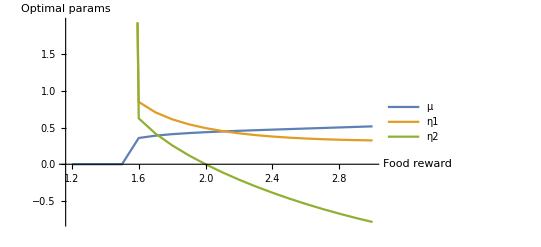

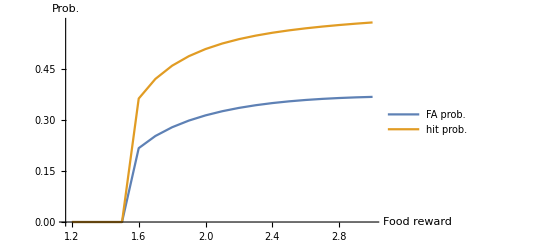

```mathematica
(*Clear["Global`*"]
Q[x_]:=1/2 Erfc[x/Sqrt[2]]
cp11= PDF[NormalDistribution[μ,1],o1];
cp12= PDF[NormalDistribution[0,1],o1];
opt = 20;
defaultLargeNot = 10;
p1Val = 0.5;
fVal = -2;
hStart =1.2;
hEnd = 3;
hInc = 0.1;
sols=Table[{minValue,argMin}=NMaximize[{(p1 (h p11+f p21)+(1-p1) (f p12+h p22)-μ^2)/. {p1->p1Val,f->fVal}/. {p01->NIntegrate[Q[-(η2+o1)] cp11,{o1,-∞,η1},MaxRecursion->opt],p11->Q[(η1-μ)],p21->NIntegrate[Q[(η2+o1)] cp11,{o1,-∞,η1},MaxRecursion->opt],p02->NIntegrate[Q[-(η2+o1-μ)] cp12,{o1,-∞,η1},MaxRecursion->opt],p12->Q[η1],p22->NIntegrate[Q[(η2+o1-μ)] cp12,{o1,-∞,η1},MaxRecursion->opt]},μ>=0},{μ,η1,η2}];
{minValue,argMin},{h,hStart,hEnd,hInc}];
totCostValues=First/@sols;
μValues=μ/. Last/@sols;
η1Values=η1/. Last/@sols;
η2Values=η2/. Last/@sols;
xValues = Range[hStart,hEnd,hInc];

faProb[μ_,η1_,η2_,h_]:=((p1 ( p21)+(1-p1) ( p12))/. {p1->p1Val,f->fVal}/. {p01->NIntegrate[Q[-(η2+o1)] PDF[NormalDistribution[μ,1],o1],{o1,-∞,η1},MaxRecursion->opt],p11->Q[(η1-μ)],p21->NIntegrate[Q[(η2+o1)] PDF[NormalDistribution[μ,1],o1],{o1,-∞,η1},MaxRecursion->opt],p02->NIntegrate[Q[-(η2+o1-μ)] PDF[NormalDistribution[0,1],o1],{o1,-∞,η1},MaxRecursion->opt],p12->Q[η1],p22->NIntegrate[Q[(η2+o1-μ)] PDF[NormalDistribution[0,1],o1],{o1,-∞,η1},MaxRecursion->opt]});
hitProb[μ_,η1_,η2_,h_]:=((p1 ( p11)+(1-p1) ( p22))/. {p1->p1Val,f->fVal}/. {p01->NIntegrate[Q[-(η2+o1)] PDF[NormalDistribution[μ,1],o1],{o1,-∞,η1},MaxRecursion->opt],p11->Q[(η1-μ)],p21->NIntegrate[Q[(η2+o1)] PDF[NormalDistribution[μ,1],o1],{o1,-∞,η1},MaxRecursion->opt],p02->NIntegrate[Q[-(η2+o1-μ)] PDF[NormalDistribution[0,1],o1],{o1,-∞,η1},MaxRecursion->opt],p12->Q[η1],p22->NIntegrate[Q[(η2+o1-μ)] PDF[NormalDistribution[0,1],o1],{o1,-∞,η1},MaxRecursion->opt]});
faProbValues=Quiet[MapThread[faProb,{μValues,η1Values,η2Values,xValues}]];
hitProbValues=Quiet[MapThread[hitProb,{μValues,η1Values,η2Values,xValues}]];
ListLinePlot[{Transpose[{xValues,μValues}],Transpose[{xValues,η1Values}],Transpose[{xValues,η2Values}]},AxesLabel->{"Food reward","Optimal params"},PlotLegends->{"μ","η1","η2"}]
ListLinePlot[{Transpose[{xValues,faProbValues}],Transpose[{xValues,hitProbValues}]},AxesLabel->{"Food reward","Prob."},PlotLegends->{"FA prob.","hit prob."}]*)
```

#### Checking if Sum is a good approximation.

```mathematica
(*ListPlot[Table[Timing[Sum[Q[-(.4+o1)] PDF[NormalDistribution[1,1],o1]*do,{o1,-5,.5,do}]],{do,10^Range[-3,-1,.2]}],AxesLabel->{"Time","Value"}]*)
```

#### Had we been assuming a miss cost.

```mathematica
(*p01[μ_,η1_,η2_] = Sum[Q[-(η2+o1)] *cp11[μ,o1]*do,{o1,dmin,η1,do}];
p02[μ_,η1_,η2_]=Sum[Q[-(η2+o1-μ)] *cp12[o1]*do,{o1,dmin,η1,do}];
rtot[μ_,η1_,η2_,h_,f_] = -μ^2 + p1(r01  p01[μ,η1,η2] + r11 p11[μ,η1] + r21 p21[μ,η1,η2])+(1-p1)(r02  p02[μ,η1,η2] + r12 p12[η1] + r22 p22[μ,η1,η2])/.{r01->0 ,r11->h,r21->f ,r02-> 0,r12->f ,r22->h };*)
```

#### Using Sum and assuming no missing cost.

```mathematica
Clear["Global`*"]
Q[x_]:=1/2 Erfc[x/Sqrt[2]]
cp11[μ_,o1_] = PDF[NormalDistribution[μ,1],o1];
cp12[o1_]= PDF[NormalDistribution[0,1],o1];
p11[μ_,η1_]=Q[(η1-μ)];
p21[μ_,η1_,η2_]=Sum[Q[(η2+o1)] *cp11[μ,o1]*do,{o1,dmin,η1,do}];
p12[η1_]=Q[η1];
p22[μ_,η1_,η2_]=Sum[Q[(η2+o1-μ)] *cp12[o1]*do,{o1,dmin,η1,do}];
faProb[μ_,η1_,η2_]:=(p1 p21[μ,η1,η2]+(1-p1) p12[η1]);
hitProb[μ_,η1_,η2_]:=(p1 p11[μ,η1]+(1-p1) p22[μ,η1,η2]);
rtot[μ_,η1_,η2_,h_,f_] = -μ^2 + h*hitProb[μ,η1,η2]+ f*faProb[μ,η1,η2];
```

```mathematica
dmin = -1;
do = .1;
hStart =1.2;
hEnd = 3;
hInc = 0.1;
```

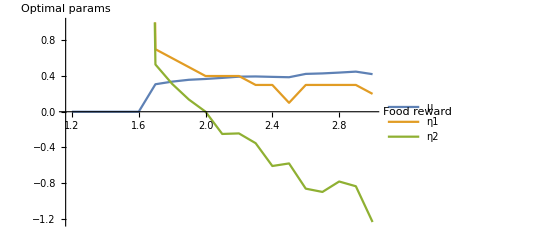

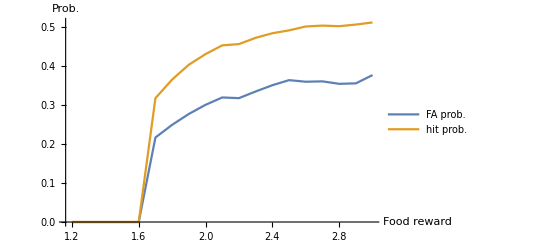

```mathematica
p1=0.5;
f=-2;

sols=Table[{minValue,argMin}=NMaximize[{rtot[μ,η1,η2,h,f],μ>=0},{μ,η1,η2}];
{minValue,argMin},{h,hStart,hEnd,hInc}];
totCostValues=First/@sols;
μValues=μ/. Last/@sols;
η1Values=η1/. Last/@sols;
η2Values=η2/. Last/@sols;
xValues = Range[hStart,hEnd,hInc];
faProbValues=Quiet[MapThread[faProb,{μValues,η1Values,η2Values}]];
hitProbValues=Quiet[MapThread[hitProb,{μValues,η1Values,η2Values}]];
ListLinePlot[{Transpose[{xValues,μValues}],Transpose[{xValues,η1Values}],Transpose[{xValues,η2Values}]},AxesLabel->{"Food reward","Optimal params"},PlotLegends->{"μ","η1","η2"},PlotRange->{All,1}]
ListLinePlot[{Transpose[{xValues,faProbValues}],Transpose[{xValues,hitProbValues}]},AxesLabel->{"Food reward","Prob."},PlotLegends->{"FA prob.","hit prob."}]
```

```mathematica
dmin = -1;
do = .1;
hStart =1.2;
hEnd = 3;
hInc = 0.1;

(*p1=0.5;
f=-2;*)
Quiet[
Manipulate[{
sols=Table[{minValue,argMin}=NMaximize[{rtot[μ,η1,η2,h,f],μ>=0},{μ,η1,η2}];
{minValue,argMin},{h,hStart,hEnd,hInc}];
totCostValues=First/@sols;
μValues=μ/. Last/@sols;
η1Values=η1/. Last/@sols;
η2Values=η2/. Last/@sols;
xValues = Range[hStart,hEnd,hInc];
faProbValues=Quiet[MapThread[faProb,{μValues,η1Values,η2Values}]];
hitProbValues=Quiet[MapThread[hitProb,{μValues,η1Values,η2Values}]];
ListLinePlot[{Transpose[{xValues,μValues}],Transpose[{xValues,η1Values}],Transpose[{xValues,η2Values}]},AxesLabel->{"Food reward","Optimal params"},PlotLegends->{"μ","η1","η2"},PlotRange->{All,1}]
ListLinePlot[{Transpose[{xValues,faProbValues}],Transpose[{xValues,hitProbValues}]},AxesLabel->{"Food reward","Prob."},PlotLegends->{"FA prob.","hit prob."}]},{{p1,0.5},0,1},{{f,-2},-4,0}]]
```

```mathematica
p1=0.5;
f=-2;

sols=Table[{minValue,argMin}=NMaximize[{rtot[μ,η1,η2,h,f],μ>=0},{μ,η1,η2}];
{minValue,argMin},{h,hStart,hEnd,hInc}];
totCostValues=First/@sols;
μValues=μ/. Last/@sols;
η1Values=η1/. Last/@sols;
η2Values=η2/. Last/@sols;
xValues = Range[hStart,hEnd,hInc];
faProbValues=Quiet[MapThread[faProb,{μValues,η1Values,η2Values}]];
hitProbValues=Quiet[MapThread[hitProb,{μValues,η1Values,η2Values}]];
ListLinePlot[{Transpose[{xValues,μValues}],Transpose[{xValues,η1Values}],Transpose[{xValues,η2Values}]},AxesLabel->{"Food reward","Optimal params"},PlotLegends->{"μ","η1","η2"},PlotRange->{All,1}]
ListLinePlot[{Transpose[{xValues,faProbValues}],Transpose[{xValues,hitProbValues}]},AxesLabel->{"Food reward","Prob."},PlotLegends->{"FA prob.","hit prob."}]
```

-Graphics-

-Graphics-

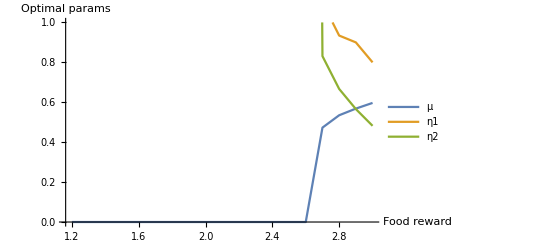

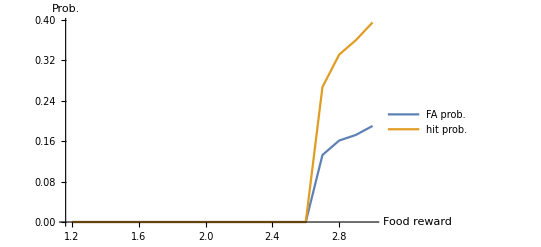

```mathematica
p1=0.5;
f=-4;

sols=Table[{minValue,argMin}=NMaximize[{rtot[μ,η1,η2,h,f],μ>=0},{μ,η1,η2}];
{minValue,argMin},{h,hStart,hEnd,hInc}];
totCostValues=First/@sols;
μValues=μ/. Last/@sols;
η1Values=η1/. Last/@sols;
η2Values=η2/. Last/@sols;
xValues = Range[hStart,hEnd,hInc];
faProbValues=Quiet[MapThread[faProb,{μValues,η1Values,η2Values}]];
hitProbValues=Quiet[MapThread[hitProb,{μValues,η1Values,η2Values}]];
ListLinePlot[{Transpose[{xValues,μValues}],Transpose[{xValues,η1Values}],Transpose[{xValues,η2Values}]},AxesLabel->{"Food reward","Optimal params"},PlotLegends->{"μ","η1","η2"},PlotRange->{All,1}]
ListLinePlot[{Transpose[{xValues,faProbValues}],Transpose[{xValues,hitProbValues}]},AxesLabel->{"Food reward","Prob."},PlotLegends->{"FA prob.","hit prob."}]
```

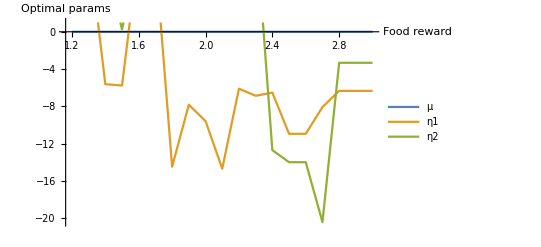

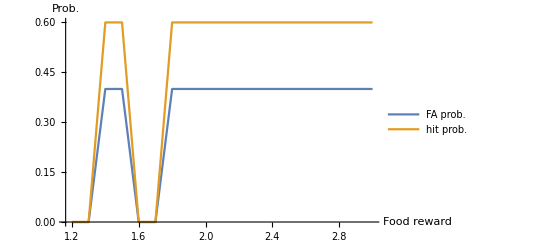

```mathematica
p1=0.6;
f=-2;

sols=Table[{minValue,argMin}=NMaximize[{rtot[μ,η1,η2,h,f],μ>=0},{μ,η1,η2}];
{minValue,argMin},{h,hStart,hEnd,hInc}];
totCostValues=First/@sols;
μValues=μ/. Last/@sols;
η1Values=η1/. Last/@sols;
η2Values=η2/. Last/@sols;
xValues = Range[hStart,hEnd,hInc];
faProbValues=Quiet[MapThread[faProb,{μValues,η1Values,η2Values}]];
hitProbValues=Quiet[MapThread[hitProb,{μValues,η1Values,η2Values}]];
ListLinePlot[{Transpose[{xValues,μValues}],Transpose[{xValues,η1Values}],Transpose[{xValues,η2Values}]},AxesLabel->{"Food reward","Optimal params"},PlotLegends->{"μ","η1","η2"},PlotRange->{All,1}]
ListLinePlot[{Transpose[{xValues,faProbValues}],Transpose[{xValues,hitProbValues}]},AxesLabel->{"Food reward","Prob."},PlotLegends->{"FA prob.","hit prob."}]
```